```mathematica
uInitial[x_]:=Exp[-3(x-2)^2];
vInitial[x_]:=NIntegrate[Re[D[uInitial[xh],{xh,2}]/(√π √(x-xh))],{xh,0,x},AccuracyGoal->20];
```

```mathematica
NIntegrate[vInitial[x],{x,-5,8},AccuracyGoal->20]
```

NIntegrate::nlim: xh = x is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00175108}. NIntegrate obtained -0.0200521 and 3.59903×10^-8 for the integral and error estimates.

-0.0200521

```mathematica
NIntegrate[uInitial[x],{x,-5,8},AccuracyGoal->20]
```

1.02333

```mathematica
Export["2init.png",Plot[{uInitial[x],vInitial[x]},{x,-5,8},PlotRange->Full,AxesLabel->{"x",""},PlotLegends->{"u_0","v_0"}]]
```

2init.png

```mathematica
vInitialPlot=Plot[vInitial[x],{x,-5,8},PlotRange->Full];
```

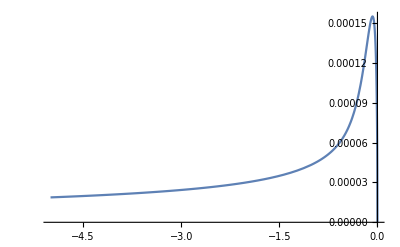

```mathematica
Plot[NIntegrate[Im[D[uInitial[xh],{xh,2}]/(√π √(x-xh))],{xh,0,x},AccuracyGoal->Infinity],{x,-5,0},PlotRange->Full]
```

```mathematica
plotList[w_,range_:Full]:=ListPlot[{Table[x,{x,-5+dx,8-dx,13/(Length[w]+1)}],w}//Transpose,PlotRange->{{-5,8},range},PlotStyle->Red];
```

201

200

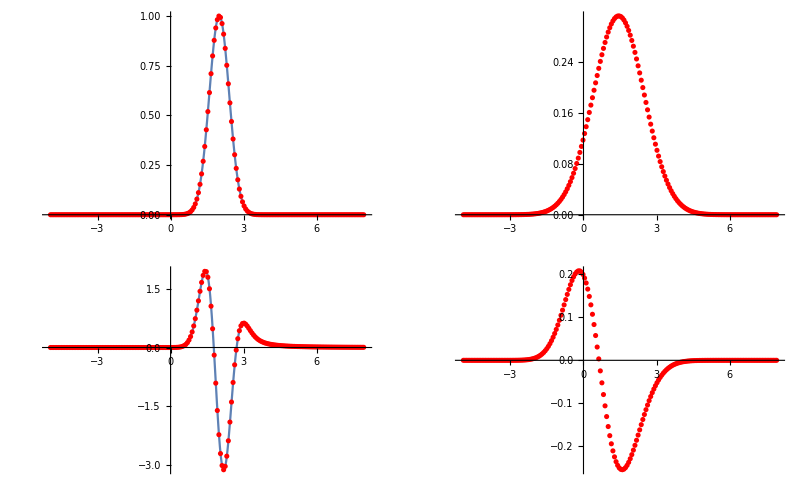

```mathematica
u=Import["/home/abe/uu/numpde/numPDE/F4a/u.dat","Table"];
v=Import["/home/abe/uu/numpde/numPDE/F4a/v.dat","Table"];
n=Length[u]-1;
m=Length[u[[1]]];
dx=(8+5)/(m+1);
dt=1/n;
n
m
GraphicsGrid[{{Show[Plot[uInitial[x],{x,-5,8},PlotRange->Full],plotList[u[[1]]]],Show[plotList[u[[-1]]]]},{Show[vInitialPlot,plotList[v[[1]]]],Show[plotList[v[[-1]]]]}},ImageSize->800]
```

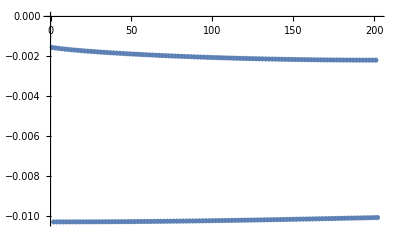

```mathematica
ListPlot[Table[v[[k]]//Mean,{k,1,Length[v],1}]]
```

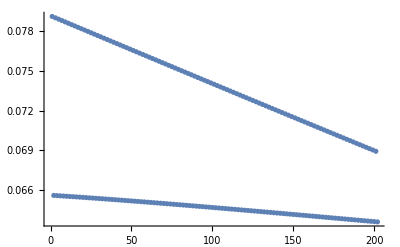

```mathematica
ListPlot[Table[u[[k]]//Mean,{k,1,Length[u],1}]]
```

```mathematica
results=GraphicsRow[{ListDensityPlot[u,PlotRange->Full,PlotLegends->Automatic,FrameLabel->{"i+1","n+1"},InterpolationOrder->0,ImageSize->Medium,PlotLabel->"u",ColorFunction->"TemperatureMap"],ListDensityPlot[v,PlotRange->Full,PlotLegends->Automatic,FrameLabel->{"i+1","n+1"},InterpolationOrder->0,ImageSize->Medium,PlotLabel->"v",ColorFunction->"TemperatureMap"]},ImageSize->900]
```

-Graphics-

```mathematica
Export["uvResult.png",results]
```

uvResult.png

```mathematica
GraphicsRow[{ListDensityPlot[u,PlotRange->Full,PlotLegends->Automatic,FrameLabel->{"i+1","n+1"},InterpolationOrder->0,ImageSize->Medium,PlotLabel->"u",ColorFunction->"TemperatureMap"],ListDensityPlot[v,PlotRange->Full,PlotLegends->Automatic,FrameLabel->{"i+1","n+1"},InterpolationOrder->0,ImageSize->Medium,PlotLabel->"v",ColorFunction->"TemperatureMap"]},ImageSize->900]
```

-Graphics-

```mathematica
v20withT00=v[[20]];
u20withT00=u[[20]];
```

```mathematica
v20withT01=v[[20]];
u20withT01=u[[20]];
```

```mathematica
v20withT02=v[[20]];
u20withT02=u[[20]];
```

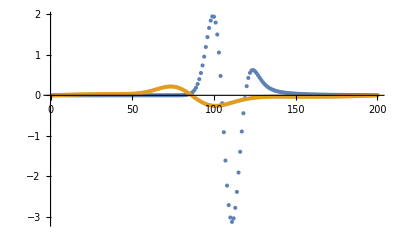

```mathematica
ListPlot[{v[[1]],v[[20]]},PlotRange->Full]
```

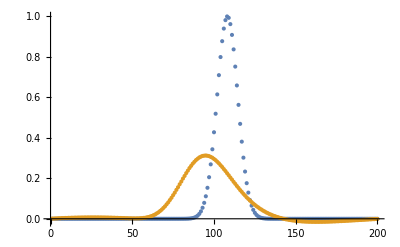

```mathematica
ListPlot[{u[[1]],u[[20]]},PlotRange->Full]
```

```mathematica
vFinals=ListPlot[{v20withT00,v20withT01,v20withT02,Table[gv,{y,1,200}]},PlotRange->Full,Joined->True,PlotLegends->{"v_final=0","v_final=0.1","v_final=0.2","fitted estimate"},AxesLabel->{"i+1","v"},PlotLabel->"v at t=1 for different v_final at t=10",ImageSize->Medium];
```

```mathematica
-0.36948628705439973 ⅇ^(-0.0021796983589234373 (-93.06891803678627+y)^2)+0.40559736585200146 ⅇ^(-0.003584576255722463 (-78.67776776214579+y)^2)
```

```mathematica
uFinals=ListPlot[{u20withT00,u20withT01,u20withT02,Table[g,{y,1,200}]},PlotRange->Full,Joined->True,PlotLegends->{"u_final=0","u_final=0.1","u_final=0.2","fitted estimate"},AxesLabel->{"i+1","u"},PlotLabel->"u at t=1 for different u_final at t=10",ImageSize->Medium];
```

```mathematica
0.31314927132111237 ⅇ^(-3 (-2.486678585705514+0.025199383606127345 y)^2)
```

```mathematica
GraphicsRow[{uFinals,vFinals},ImageSize->1000]
```

-Graphics-

```mathematica
Export["uvFinals.png",GraphicsRow[{uFinals,vFinals},ImageSize->1000]]
```

uvFinals.png

```mathematica
Export["vFinals.png",vFinals]
```

vFinals.png

```mathematica
Export["uFinals.png",uFinals]
```

uFinals.png

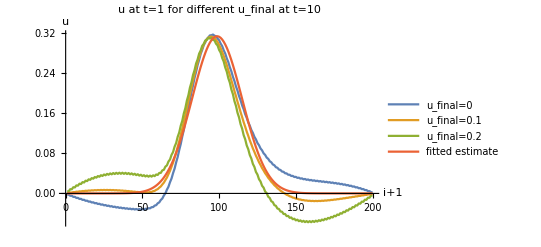

```mathematica
uFinals
```

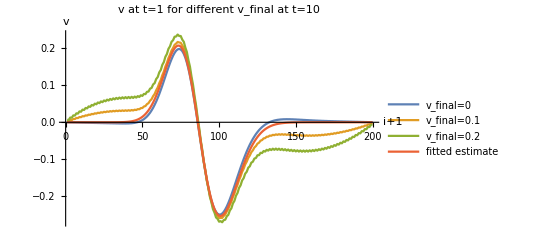

```mathematica
vFinals
```

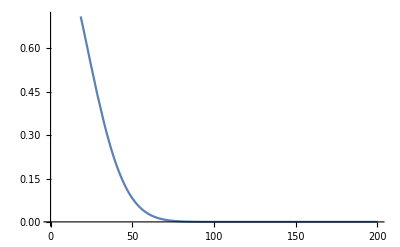

```mathematica
Plot[Exp[-0.001(x)^2],{x,0,200}]
```

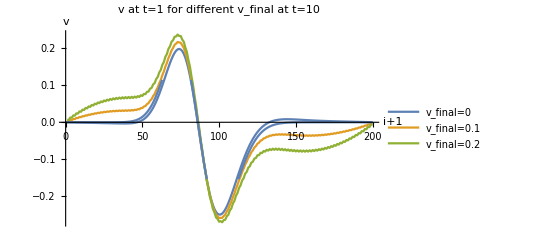

```mathematica
Show[vFinals,Plot[gv,{y,0,200}]]
```

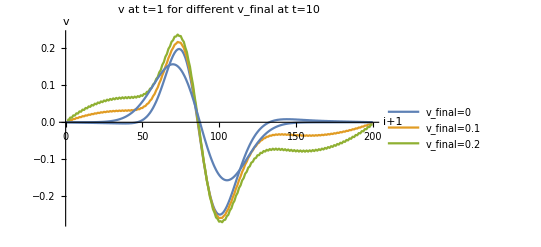

```mathematica
Show[vFinals,Plot[0.2Exp[-0.002(x-75.0)^2]-0.2Exp[-0.002(x-100.0)^2],{x,0,200}]]
```

```mathematica
paramsv=FindFit[(v20withT00+v20withT01)/2,a Exp[b(y-c)^2]-d Exp[e(y-F)^2],{{a,0.2},{b,-0.002},{c,75},{d,-0.2},{e,-0.002},{F,100}},y]
```

{a→0.405597,b→-0.00358458,c→78.6778,d→0.369486,e→-0.0021797,F→93.0689}

```mathematica
gv=(a Exp[b(y-c)^2]-d Exp[e(y-F)^2]/.paramsv)
```

-0.369486 ⅇ^(-0.0021797 (-93.0689+y)^2)+0.405597 ⅇ^(-0.00358458 (-78.6778+y)^2)

```mathematica
uFinals
```

-Graphics-

```mathematica
Exp[-3(x-2)^2];
```

{a→0.313149,b→0.0251994,c→2.48668}

0.313149 ⅇ^(-3 (-2.48668+0.0251994 y)^2)

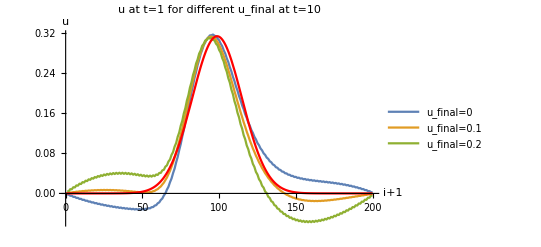

{a→0.0000575233,b→0.0551136}

```mathematica
f[a_,b_,c_]:=a Exp[-3(b y-c)^2];
params=FindFit[(u20withT00 2+0u20withT01)/2,f[a,b,c],{{a,0.3},{b,1/40},{c,2.4}},y]
g=f[a,b,c]/. params
Show[uFinals,Plot[g,{y,0,200},PlotStyle->Red]]
```

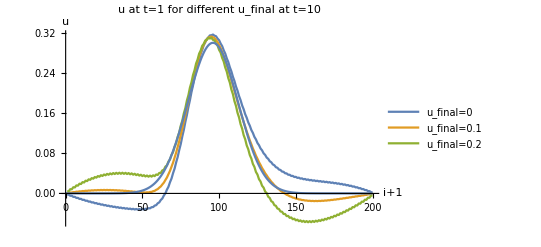

```mathematica
Show[uFinals,Plot[.3Exp[-3(x/40-2.4)^2],{x,0,200}]]
```

```mathematica
(*GraphicsGrid[{{ListPlot3D[Partition[u,2][[All,1]],PlotRange->Full],ListPlot3D[Partition[v,2][[All,1]],PlotRange->Full]},{ListPlot3D[Partition[u,2][[All,2]],PlotRange->Full],ListPlot3D[Partition[v,2][[All,2]],PlotRange->Full]}},ImageSize->900]*)
GraphicsRow[{ListPlot3D[u,PlotRange->Full],ListPlot3D[v,PlotRange->Full]},ImageSize->900]
```

-Graphics-

```mathematica
oddu=Partition[u,2][[All,1]];
evenu=Partition[u,2][[All,2]];
smoothoddu=Table[(oddu[[k]]+oddu[[k+1]])/2,{k,1,Length[oddu]-1}];
```

```mathematica
Export["errorFinal.png",ListPlot3D[evenu[[;;-2]]-smoothoddu,PlotLabel->"Estimated error in u",AxesLabel->{"i+1","n+1"}]]
```

errorFinal.png

```mathematica
ListPlot3D[evenu[[;;-2]]-smoothoddu,PlotLabel->"Estimated error in u",AxesLabel->{"i+1","n+1"}]
```

-Graphics3D-

```mathematica
0.05/0.3
```

0.166667

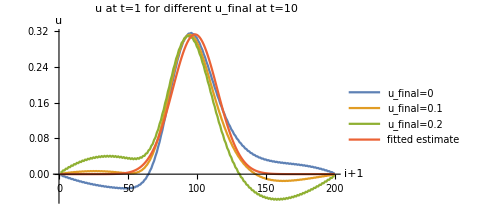

```mathematica
uFinals
```

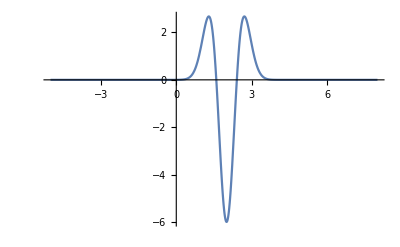

```mathematica
Plot[D[uInitial[y],{y,2}]/.{y->x},{x,-5,8},PlotRange->Full]
```

```mathematica
ListPlot3D[{oddu,evenu},PlotRange->Full]
```

-Graphics3D-

```mathematica
Manipulate[GraphicsRow[{plotList[u[[n]],{-0.4,1.1}],plotList[v[[n]],{-2.5,2}]},ImageSize->800],{n,1,Length[u],1}]
```